# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## 1. Individuals

## Generating Population

### Nodes

#### kmActivationFunc

```mathematica
kmActivationFunc[id_]:=
Switch[id,
0, #&,
1,Tanh[#]&,
2,LogisticSigmoid[#]&,
3,Sin[#]&,
4,UnitStep[#]&,
5,Ramp[#]&
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,layer_,totalFuncs_:5]:=<|
"nodeId"->id,
"layer"->layer,
"inputSum"->0,
"bias"->RandomReal[{-1,1}],
"activationFunc"->RandomInteger[totalFuncs],
"output"->0
|>
```

```mathematica
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1,1]
kmNodeOutput[%,{kmNode[2,1]~Join~<|"output"->12|>,kmNode[3,2]~Join~<|"output"->2|>}]
```

<|nodeId→1,layer→1,inputSum→0,bias→-0.280382,activationFunc→5,output→0|>

<|nodeId→1,layer→1,inputSum→14,bias→-0.280382,activationFunc→5,output→13.7196|>

```mathematica
kmNodeOutput[kmNode[1,1],{}]
```

<|nodeId→1,layer→1,inputSum→0,bias→-0.423433,activationFunc→3,output→-0.423433|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmIndividual]
kmIndividual[input_,output_,hidden_:0]:=
<|
"input"->input,
"output"->output,
"total"->input+output,
"fitness"->∞,
"nodes"->Join[
kmNode[#,1,0]&/@Range[input],
kmNode[#,2]&/@(input+Range[output])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[input],
Range[input+1,input+output]
],1])
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,size_:10,options___]:=<|
"input"->in,
"output"->out,
"best"-><|"fitness"->+∞|>,
"history"->{},
"size"->size,
(*"inovations"->{},*)
"individuals"->Array[kmIndividual[in,out]&,size],
"state"->{0,0,0},
"params"-><|
"addConnRate"->0.8,
"removeConnRate"->0.1,
"addNodeRate"->0.7,
"removeNodeRate"->0.05,
"crossOverRate"->0.6
|>
|>~Join~options
```

### Tests

```mathematica
testPop=kmPopulation[2,3];
```

## Individual decoding

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
First@FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,3]
```

3

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Flatten
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

```mathematica
Flatten@Last@Reap[(If[4==#1["output"],Sow[#1["input"]]]&)/@{<|"input"->2,"output"->4,"weight"->0.46823495271841686,"enabled"->False,"inovation"->25|>,<|"input"->4,"output"->3,"weight"->-0.9862659750123437,"enabled"->True,"inovation"->31|>,<|"input"->1,"output"->3,"weight"->0.7495483633226465,"enabled"->True,"inovation"->13|>,<|"input"->2,"output"->3,"weight"->0.7957445269342958,"enabled"->False,"inovation"->18|>,<|"input"->5,"output"->4,"weight"->0.5820582065734872,"enabled"->True,"inovation"->49|>};]
```

{2,5}

```mathematica
popClassTest["individuals"][[9]]
```

<|input→2,output→1,total→5,fitness→4.88136,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.0656402,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.653727,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.463402,activationFunc→5,output→0|>,<|nodeId→4,layer→3,inputSum→0,bias→-0.959485,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.272139,activationFunc→2,output→0|>},connections→{<|input→2,output→4,weight→0.468235,enabled→False,inovation→25|>,<|input→4,output→3,weight→-0.986266,enabled→True,inovation→31|>,<|input→1,output→3,weight→0.749548,enabled→True,inovation→13|>,<|input→2,output→3,weight→0.795745,enabled→False,inovation→18|>,<|input→5,output→4,weight→0.582058,enabled→True,inovation→49|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.0656402,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.653727,activationFunc→0,output→0|>},{<|nodeId→5,layer→2,inputSum→0,bias→-0.272139,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.463402,activationFunc→5,output→0|>,<|nodeId→4,layer→3,inputSum→0,bias→-0.959485,activationFunc→2,output→0|>}}|>

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### Prepare for evaluation

#### kmNodesToLayers

```mathematica
ClearAll[kmNodesToLayers]
kmNodesToLayers[individual_]:=
Module[
{maxLayer=Max[individual[["nodes",All,"layer"]]],
nodes
},
Join[individual,
<|
"maxLayer"->maxLayer,
"nodesLayered"->(Function[{layer},Select[individual["nodes"],#["layer"]==layer&]]/@Range[maxLayer])
|>
]
]
```

#### kmIndividualsToLayers

```mathematica
ClearAll[kmIndividualsPrepare]
SetAttributes[kmIndividualsPrepare,HoldFirst]
kmIndividualsPrepare[population_]:=
population⟦"individuals"⟧=kmNodesToLayers[#]&/@population["individuals"]
```

```mathematica
kmIndividualsPrepare[testPop];
```

#### kmInitFirstLayer

```mathematica
ClearAll[kmInitFirstLayer]
kmInitFirstLayer[nodes_,inputs_List]:=
MapThread[Join[#1,<|"output"->#2|>]&,{SortBy[nodes,#["nodeId"]&],inputs}]
```

#### kmGetNodesLayered

```mathematica
ClearAll[kmGetNodesLayered]
kmGetNodesLayered[individual_,nodeIds_]:=
Flatten[Function[{nodeId},Select[individual["nodesLayered"]//Flatten,#["nodeId"]==nodeId&,1]]/@nodeIds]
```

#### kmInNodesLayered

```mathematica
ClearAll[kmInNodesLayered]
kmInNodesLayered[individual_,node_]:=kmGetNodesLayered[individual,kmInNodes[node["nodeId"],individual["connections"]]]
```

```mathematica
kmInNodesLayered[testPop["individuals"][[1]],<|"nodeId"->3,"layer"->1,"inputSum"->0,"bias"->-0.012840107337042994,"activationFunc"->0,"output"->1|>]
```

{<|nodeId→6,layer→2,inputSum→0,bias→-0.275825,activationFunc→1,output→0|>,<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>}

### Evaluation

#### kmIndividualEvaluate

```mathematica
ClearAll[kmIndividualEvaluate]
kmIndividualEvaluate[individual_,inputs_:{_,_}]:=
Module[
{individualCopy=individual},
individualCopy[["nodesLayered",1]]=kmInitFirstLayer[individualCopy["nodesLayered"]//First,inputs];
Function[{layer},
individualCopy[["nodesLayered",layer]]=
Function[{node},
kmNodeOutput[node,kmInNodesLayered[individualCopy,node]]
]/@individualCopy[["nodesLayered",layer]]
]/@Range[2,individual["maxLayer"]];
kmGetNodesLayered[individualCopy,Range[#+1,#+individual["output"]]&[individual["input"]]]⟦All,"output"⟧
]
```

```mathematica
kmIndividualEvaluate[popClassTest["individuals"][[9]],{.1,.2}]
```

{-0.163402}

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,layer_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,layer},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

Graph

### Population viewing

## Population operations

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧
},
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦in,"layer"⟧<individual["nodes"]⟦out,"layer"⟧,{kmConnection[conn]},{}]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### tests

```mathematica
kmAddNode[testPop,1,1]
kmAddConnection[testPop,1,{1,6}]
```

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.614519,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.319459,activationFunc→4,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→-0.275825,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.141196,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.0933813,enabled→True,inovation→48|>,<|input→1,output→3,weight→0.745066,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.0945409,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.361019,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.504988,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.277952,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.547047,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.614519,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.319459,activationFunc→4,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→-0.275825,activationFunc→1,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>}}|>

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.614519,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.319459,activationFunc→4,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→-0.275825,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.141196,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.0933813,enabled→True,inovation→48|>,<|input→1,output→3,weight→0.745066,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.0945409,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.361019,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.504988,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.277952,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.547047,enabled→True,inovation→33|>,<|input→1,output→6,weight→-0.890419,enabled→True,inovation→34|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.614519,activationFunc→2,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.319459,activationFunc→4,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→-0.275825,activationFunc→1,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>}}|>

## Population mutations

### kmMutateNodes

```mathematica
ClearAll[kmMutateNodes]
SetAttributes[kmMutateNodes,HoldFirst]
kmMutateNodes[population_,individualId_]:= 
If[
RandomReal[]<population["params","addNodeRate"],
population["state"]=population["state"]+{0,1,0};
kmAddNode[population,individualId,RandomInteger[{1,Length[population⟦"individuals",individualId,"connections"⟧]}]],
population[["individuals",individualId]]
]
```

### kmMutateConnections

```mathematica
ClearAll[kmMutateConnections]
SetAttributes[kmMutateConnections,HoldFirst]
kmMutateConnections[population_,individualId_]:= 
If[
RandomReal[]<population["params","addConnRate"],
population["state"]=population["state"]+{0,0,1};
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧],
population[["individuals",individualId]]
]
```

### kmCrossover

#### kmNodesFromConns

```mathematica
kmNodesFromConnections[connections_]:= 
Union[Part[connections,All,"input"],Part[connections,All,"output"]]
```

#### kmCrossover

```mathematica
kmCrossover[parent1_,parent2_]:= 
Module[
{conns1,conns2, nodes1,nodes2, 
separator= RandomChoice[
Join[parent1["connections"],parent2["connections"]]
]["inovation"]
},
conns1 =Select[parent1["connections"],#["inovation"]≤separator&] ;
conns2=Select[parent2["connections"],#["inovation"]>separator&];
nodes1=kmNodesFromConnections[conns1];
nodes2=Complement[kmNodesFromConnections[conns2],nodes1];
kmNodesToLayers@<|
"input"->parent1["input"],
"output"->parent1["output"],
"total"->Length[Join[nodes1,nodes2]],
"fitness"->∞,
"nodes"->Join[parent1["nodes"]⟦nodes1⟧,parent2["nodes"]⟦nodes2⟧],
"connections"->Join[conns1,conns2]
|>
]
```

```mathematica
kmCrossover[testPop[["individuals",1]],testPop[["individuals",3]]]
```

<|input→2,output→3,total→5,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.854505,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.116881,activationFunc→4,output→0|>},connections→{<|input→1,output→3,weight→0.745066,enabled→False,inovation→13|>,<|input→2,output→3,weight→0.504988,enabled→True,inovation→18|>,<|input→1,output→4,weight→0.246895,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.644287,enabled→True,inovation→26|>,<|input→2,output→4,weight→-0.0861387,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.221945,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.98348,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.341658,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.854505,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.116881,activationFunc→4,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.190813,activationFunc→3,output→0|>}}|>

## Population evolution

### Fitness

#### kmAssessFitnessAll

```mathematica
ClearAll[kmAssessFitnessAll]
SetAttributes[kmAssessFitnessAll,HoldFirst]
kmAssessFitnessAll[population_Symbol,fitness_Function]:=Module[
{min},
min=Min[population[["individuals",All,"fitness"]]=(fitness/@population["individuals"])];

If[min<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",Position[population[["individuals",All,"fitness"]],min]⟦1,1⟧⟧
]
]
]
```

#### kmAssessFitness

```mathematica
ClearAll[kmAssessFitness]
SetAttributes[kmAssessFitness,HoldFirst]
kmAssessFitness[population_Symbol,fitness_Function,individualId_]:=Module[
{fit},
fit=population[["individuals",individualId,"fitness"]]=fitness@population[["individuals",individualId]];
If[fit<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",individualId⟧
]
]
]
```

### Elimination

```mathematica
SetAttributes[kmElimination,HoldFirst]
kmElimination[population_,replaceIndividual_]:=
Block[{
index=RandomChoice[(Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
},
(*Print[index];*)
population⟦"individuals",index⟧=replaceIndividual;
index
]
```

### Selection

```mathematica
SetAttributes[kmSelection,HoldFirst]
kmSelection[population_]:=
RandomChoice[(#/Total[#]&)@(1/Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
```

### Evolution

```mathematica
ClearAll[kmEvolveOne]
SetAttributes[kmEvolveOne,HoldFirst]
kmEvolveOne[population_,fitness_]:=
Catch[
Block[{individualId=kmSelection[population]},
(*kmAssessFitness[population,fitness];*)
Which[
RandomReal[]<population⟦"params","crossOverRate"⟧/4,
population["state"]=population["state"]+{1,0,0};
kmAssessFitness[population,fitness,kmElimination[population,#]]&[
kmCrossover[population⟦"individuals",individualId⟧,
population⟦"individuals",RandomInteger[{1,population["size"]}]⟧
]];,
RandomReal[]<population⟦"params","addNodeRate"⟧/8,
kmAssessFitness[population,fitness,kmElimination[population,kmMutateNodes[population,individualId]]];,
RandomReal[]<population⟦"params","addConnRate"⟧/8,
kmAssessFitness[population,fitness,kmElimination[population,kmMutateConnections[population,individualId]]];
];
individualId
]
];
```

## Test Task 1 - simple binary Classification in 2D

### kmClassificationTask – generate a task

```mathematica
ClearAll[kmClassificationTask]
kmClassificationTask[function_,testersNumber_:50,rangeX_:{0,6},rangeY_:{-1,1}]:=
Block[{targets,
testers
},
testers =Thread[ {RandomReal[rangeX,testersNumber],RandomReal[rangeY,testersNumber]}];
targets=If[function[#1]>#2,1,0]&@@@testers;
<|"function"->function,"testers"->testers,"targets"->targets,"rangeX"->rangeX, "rangeY"->rangeY|>
]
```

```mathematica
kmClassificationTask[Sin]
```

<|function→Sin,testers→{{1.51488,0.64631},{0.47089,0.876597},{2.10084,0.146755},{2.74262,-0.33766},{1.21189,0.301378},{4.0799,0.761358},{0.731018,-0.0293363},{0.00773929,-0.157099},{1.9184,0.224236},{3.45283,0.206023},{4.86045,-0.482809},{3.04254,0.226359},{1.71855,-0.0778491},{2.84324,0.182088},{3.8776,0.0484514},{1.21277,-0.381521},{5.41766,0.28018},{3.27422,-0.858155},{2.33583,0.901986},{1.28289,0.45366},{2.21645,-0.0459496},{5.46989,0.147686},{4.20489,-0.528843},{0.453846,-0.421514},{4.19405,-0.465721},{0.415198,-0.0402607},{1.49797,0.325844},{5.37998,-0.924732},{2.77624,0.194242},{4.93535,-0.558812},{3.93408,0.861082},{0.149698,0.689805},{0.0019217,-0.441641},{4.19898,-0.54295},{1.61612,-0.950189},{4.93437,-0.639477},{3.51061,-0.276899},{2.2489,0.684065},{3.40266,-0.0886894},{0.733396,0.075356},{4.83061,0.331864},{0.295072,-0.580468},{2.44969,0.28228},{5.79184,0.125646},{2.91843,-0.847141},{2.12497,0.36708},{5.55662,-0.923568},{5.38,0.149356},{3.0197,-0.742974},{5.35262,0.0663476}},targets→{1,0,1,1,1,0,1,1,1,0,0,0,1,1,0,1,0,1,0,1,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,1,1,0,1,1,1,0,1,0},rangeX→{0,6},rangeY→{-1,1}|>

### Additional functions

#### kmPredictionToAnswer

```mathematica
ClearAll[kmPredictionToAnswer]
SetAttributes[kmPredictionToAnswer,Listable]
kmPredictionToAnswer[prediction_]:=If[prediction>0.5,1,0]
```

#### kmClassificationAccuracy

```mathematica
kmClassificationAccuracy[targets_,predictions_]:=N@EuclideanDistance[targets,predictions]
```

#### kmClassificationPredictions

```mathematica
kmClassificationPredictions[task_,individual_]:=LogisticSigmoid[First@kmIndividualEvaluate[individual,#]&/@task["testers"]]
```

#### kmClassificationFitness

```mathematica
kmClassificationFitness[task_]:=With[
{targets=task["targets"],testers=task["testers"]},
Function[{individual},
N@EuclideanDistance[targets,LogisticSigmoid@kmIndividualEvaluate[individual,#]&/@testers]
]
]
```

### kmShowPredictions

#### NonZeroQ

```mathematica
ClearAll[NonZeroQ]
NonZeroQ[n_]:=(n=!=0)&&NumberQ[n]
```

#### kmShowTestersEpilog

```mathematica
ClearAll[kmShowTestersEpilog]
kmShowTestersEpilog[testers_,targets_,predictions_]:=
{AbsolutePointSize[11],{
Red,Point@Extract[testers,Position[targets-#,_?NonZeroQ]],
White,Point@Extract[testers,Position[targets-#,0]]},
AbsolutePointSize[7],{
Darker@Yellow,Point@Extract[testers,Position[#,0]],
Blue,Point@Extract[testers,Position[#,1]]
}
}&[kmPredictionToAnswer[predictions]]
```

#### kmShowPredictions

```mathematica
ClearAll[kmShowPredictions]
kmShowPredictions[task_,predictions_]:=
With[{
function =task["function"]
},
Labeled[
Plot[function[x],{x,Sequence@@task["rangeX"]},
Epilog->kmShowTestersEpilog[task["testers"],task["targets"],predictions],
PlotRange->{task["rangeX"],task["rangeY"]},AspectRatio->1,Axes->True,
Background->LightGray
],
"Error: "<>ToString@kmClassificationAccuracy[task["targets"],predictions]
]

]
```

```mathematica
kmShowPredictions[classTest,RandomReal[{0,1},50]]
```

Extract::partw: Part 2 of classTest[testers] does not exist.

Extract::partw: Part 3 of classTest[testers] does not exist.

Extract::partw: Part 2 of classTest[testers] does not exist.

General::stop: Further output of Extract::partw will be suppressed during this calculation.

Plot::pllim: Range specification {x,rangeX} is not of the form {x, xmin, xmax}.

Plot[classTest[function][x],{x,Sequence@@classTest[rangeX]},Epilog→kmShowTestersEpilog[classTest[testers],classTest[targets],{0.422929,0.528321,0.488923,0.768233,0.743303,0.974732,0.146927,0.948586,0.541466,0.0193788,0.516504,0.706929,0.382562,0.997173,0.616438,0.738488,0.487658,0.00860656,0.273715,0.445627,0.197162,0.106889,0.342145,0.332562,0.25591,0.906289,0.585301,0.331185,0.921643,0.399016,0.806955,0.552293,0.0720858,0.746921,0.268279,0.296992,0.254081,0.297569,0.300852,0.377724,0.455311,0.11294,0.504303,0.036197,0.295647,0.68473,0.0597614,0.3388,0.0931364,0.190698}],PlotRange→{classTest[rangeX],classTest[rangeY]},AspectRatio→1,Axes→True,Background→LightGray]Error:                                         2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                     2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                    2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                      2                                     2                                      2                                      2                                      2                                      2                                     2                                      2                                       2                                       2                                       2                                      2                                       2                                        2
Sqrt[Abs[-0.997173 + classTest[targets]]  + Abs[-0.974732 + classTest[targets]]  + Abs[-0.948586 + classTest[targets]]  + Abs[-0.921643 + classTest[targets]]  + Abs[-0.906289 + classTest[targets]]  + Abs[-0.806955 + classTest[targets]]  + Abs[-0.768233 + classTest[targets]]  + Abs[-0.746921 + classTest[targets]]  + Abs[-0.743303 + classTest[targets]]  + Abs[-0.738488 + classTest[targets]]  + Abs[-0.706929 + classTest[targets]]  + Abs[-0.68473 + classTest[targets]]  + Abs[-0.616438 + classTest[targets]]  + Abs[-0.585301 + classTest[targets]]  + Abs[-0.552293 + classTest[targets]]  + Abs[-0.541466 + classTest[targets]]  + Abs[-0.528321 + classTest[targets]]  + Abs[-0.516504 + classTest[targets]]  + Abs[-0.504303 + classTest[targets]]  + Abs[-0.488923 + classTest[targets]]  + Abs[-0.487658 + classTest[targets]]  + Abs[-0.455311 + classTest[targets]]  + Abs[-0.445627 + classTest[targets]]  + Abs[-0.422929 + classTest[targets]]  + Abs[-0.399016 + classTest[targets]]  + Abs[-0.382562 + classTest[targets]]  + Abs[-0.377724 + classTest[targets]]  + Abs[-0.342145 + classTest[targets]]  + Abs[-0.3388 + classTest[targets]]  + Abs[-0.332562 + classTest[targets]]  + Abs[-0.331185 + classTest[targets]]  + Abs[-0.300852 + classTest[targets]]  + Abs[-0.297569 + classTest[targets]]  + Abs[-0.296992 + classTest[targets]]  + Abs[-0.295647 + classTest[targets]]  + Abs[-0.273715 + classTest[targets]]  + Abs[-0.268279 + classTest[targets]]  + Abs[-0.25591 + classTest[targets]]  + Abs[-0.254081 + classTest[targets]]  + Abs[-0.197162 + classTest[targets]]  + Abs[-0.190698 + classTest[targets]]  + Abs[-0.146927 + classTest[targets]]  + Abs[-0.11294 + classTest[targets]]  + Abs[-0.106889 + classTest[targets]]  + Abs[-0.0931364 + classTest[targets]]  + Abs[-0.0720858 + classTest[targets]]  + Abs[-0.0597614 + classTest[targets]]  + Abs[-0.036197 + classTest[targets]]  + Abs[-0.0193788 + classTest[targets]]  + Abs[-0.00860656 + classTest[targets]] ]

### Test

```mathematica
classTest=kmClassificationTask[Sin];
fitnessClassTest=kmClassificationFitness[classTest];

popClassTest=kmPopulation[2,1,20];
kmIndividualsPrepare[popClassTest];
kmAssessFitnessAll[popClassTest,fitnessClassTest];
```

{2.85015,3.92875,2.73328,3.12016,3.7539,3.92283,3.12016,4.43623,3.7708,3.99039,3.69654,2.72156,3.37171,3.92283,3.92283,3.12016,3.92283,4.63416,3.12016,3.69654}

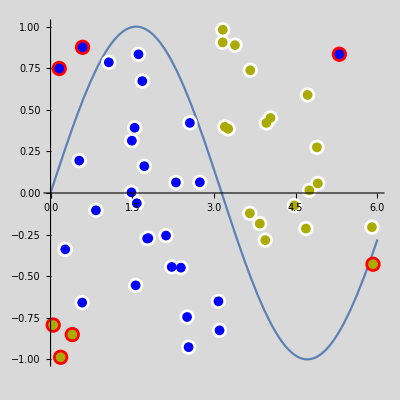
-Graphics-Error: 2.72156

```mathematica
popClassTest[["individuals",All,"fitness"]]
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
```

```mathematica
popClassTest["history"]
```

{<|input→2,output→1,total→3,fitness→2.72156,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.693598,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.38481,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→0.276576,activationFunc→3,output→0|>},connections→{<|input→1,output→3,weight→0.450387,enabled→True,inovation→13|>,<|input→2,output→3,weight→0.680464,enabled→True,inovation→18|>},maxLayer→2,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.693598,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.38481,activationFunc→0,output→0|>},{<|nodeId→3,layer→2,inputSum→0,bias→0.276576,activationFunc→3,output→0|>}}|>}

```mathematica
kmIndividualEvaluate[popClassTest["individuals"][[7]],{1,2}]
```

{3.74722}

```mathematica
popClassTest["individuals"][[7]]
```

<|input→2,output→1,total→3,fitness→4.87629,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.629443,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.826493,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→0.747217,activationFunc→5,output→0|>},connections→{<|input→1,output→3,weight→-0.220811,enabled→True,inovation→13|>,<|input→2,output→3,weight→0.972385,enabled→True,inovation→18|>},maxLayer→2,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.629443,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.826493,activationFunc→0,output→0|>},{<|nodeId→3,layer→2,inputSum→0,bias→0.747217,activationFunc→5,output→0|>}}|>

```mathematica
Monitor[Do[kmEvolveOne[popClassTest,fitnessClassTest],{i,20}],i]
```